```mathematica
ld=2.59020683 10^13
```

2.59021×10^13

```mathematica
RotMat[a_,b_,c_]:=Evaluate[{{Cos[c] Cos[a]-Sin[c] Cos[b] Sin[a],-Cos[c] Sin[a]-Sin[c] Cos[b] Cos[a],Sin[a] Sin[b]},{Sin[c] Cos[a]+Cos[c] Cos[b] Sin[a],-Sin[c] Sin[a]+Cos[c] Cos[b] Cos[a],-Cos[a] Sin[b]},{Sin[b] Sin[a],Sin[b] Cos[a], Cos[b]}}]
```

```mathematica
a=RotMat[65°,135°,-40°]//N
```

{{-0.0881902,-0.88636,0.640856},{-0.762578,0.353642,-0.298836},{0.640856,0.298836,-0.707107}}

```mathematica
R={l1[6 ld,0.88] Cos[x],l2[6 ld, 0.88] Sin[x],0}
```

{Cos[x] l1[1.55412×10^14,0.88],l2[1.55412×10^14,0.88] Sin[x],0}

```mathematica
Series[y-e Sin[y],{y,0,10}]//InputForm
```

SeriesData[y, 0, {1 - e, 0, 
  e/6, 0, -e/120, 0, e/5040, 
  0, -e/362880}, 1, 11, 1]

```mathematica
c=3*10^8
```

300000000

```mathematica
EccAnom[t_,e_,v_,a_,n_]:=FromDigits[Reverse[CoefficientList[Normal[InverseSeries[Series[(a*(y-e Sin[y]))/v,{y,0,n}]]],y]],k]/.k-> t
```

```mathematica
Ellipse[a_,e_,E_]:={a(1-e Cos[E]),a √(1-e^2) Sin[E],0}
Ellipse2[t_,e_,v_,a_,n_]:=With[{ecc=FromDigits[Reverse[CoefficientList[Normal[InverseSeries[Series[(a*(y-e Sin[y]))/v,{y,0,n}]]],y]],k]/.k-> t},Ellipse[a,e,ecc]]
```

```mathematica
ParametricPlot3D[{Ellipse2[t,0.88,0.0058 c,6 ld,10]},{t,0,10^7}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Porb[v_,a_]:=(2 π a)/v
```

```mathematica
RotMat[65°,135°,-40°].Ellipse[6 ld, 0.88, a]//N
```

{-1.37058×10^13 (1.-0.88 Cos[a])-6.54283×10^13 Sin[a],-1.18514×10^14 (1.-0.88 Cos[a])+2.61047×10^13 Sin[a],9.9597×10^13 (1.-0.88 Cos[a])+2.20591×10^13 Sin[a]}

```mathematica
ParametricPlot3D[Ellipse[6 ld, 0.88, d],{d,0°,360°}]
```

-Graphics3D-

-Graphics3D-

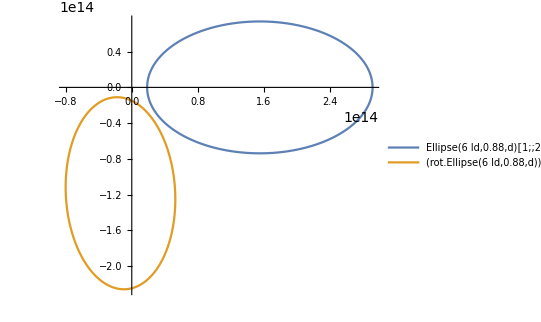

```mathematica
ParametricPlot3D[{Ellipse[6 ld, 0.88, d],rot.Ellipse[6 ld, 0.88, d]},{d,0°,360°},PlotLegends->"Expressions"]
ParametricPlot[{Ellipse[6 ld, 0.88, d][[;;2]],(rot.Ellipse[6 ld, 0.88, d])[[;;2]]},{d,0°,360°},PlotLegends->"Expressions"]
```

```mathematica
FullSimplify[Normal[InverseSeries[Series[x-ϵ Sin[x],{x,0,10}]]]]/.{x-> 5,ϵ-> 0.88}
```

4.83676×10^16

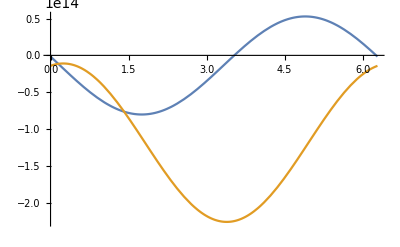

```mathematica
Plot[{(rot.Ellipse[6 ld, 0.88, d])[[1]],(rot.Ellipse[6 ld, 0.88, d])[[2]]},{d,0°,360°}]
```

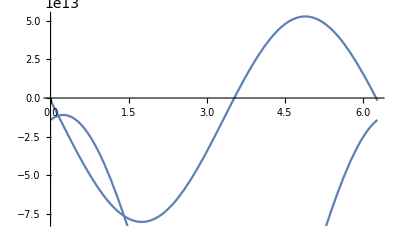

```mathematica
Show[{p1,p2}]
```

```mathematica
Manipulate[ParametricPlot3D[{Ellipse[a, e, d],RotMat[ω,i,Ω].Ellipse[a, e, d]},{d,0°,360°},PlotLegends->{"self frame","earth frame"}],{a,10^8,10^15,50},{e,-5,5},{ω,0°,360°},{i,0°,360°},{Ω,0°,360°}]
```

Damn. There was EulerMatrix Function the whole time. facepalm.